lpw

```mathematica
(* Mathematica notebook for trajetory in linear polarized plane wave. Following [Gibbon]'s lecture 3
  date : 10/12/2018
  author: Óscar L. Amaro
*)
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
imgsize=400;asp=1.0;tck=0.01;sz=30; dsh=0.05;
```

{0.3,1.,3.}

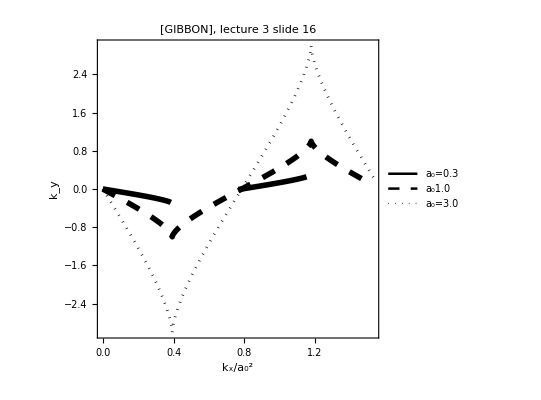
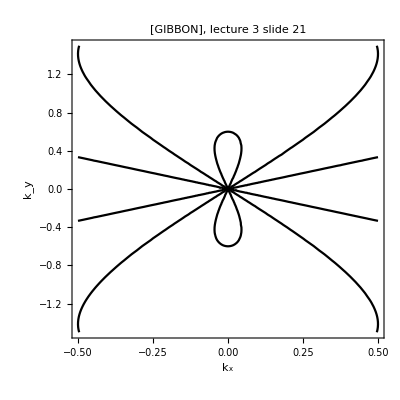

```mathematica
δ=-1;ω=1;k=1;x=1;
ϕ[t_]:=ω*t-k*x
data[a0_]:=Module[{tab},
tab=Table[N[
{
1/4*(ϕ[t]+(2δ^2-1)/2*Sin[2*ϕ[t]]),
δ*a0*Sin[ϕ[t]]
}],{t,1,7.2,0.05}];
Return [tab]
]
plt1=ListLinePlot[
{data[0.3],
data[1.0],
data[3]
},

PlotStyle->{
Directive[Black,Dashing[1],Thickness[tck]],
Directive[Black,Dashing[dsh/2],Thickness[tck]],
Directive[Black,Dotted,Thickness[tck/2]]
},
PlotLabel->"[GIBBON], lecture 3 slide 16",LabelStyle->Directive[Bold,FontSize->20],
ImageSize->imgsize,AspectRatio->asp,
Frame->{True,True},FrameLabel->{"k_x/a_0^2","k_y"},FrameStyle->Directive[Thick],
PlotLegends->Placed[LineLegend[{"a_0=0.3","a_01.0","a_0=3.0"},LabelStyle->{Black,Bold,18},LegendLayout->{"Column",1}],{0.25,0.75}]];

q={0.3,1.0,3.0}
plt2=ContourPlot[
16x^2-y^2*(4*q^2-y^2)==0,{x,-0.5,0.5},{y,-1.5,1.5},
ContourStyle->Black,
PlotLabel->"[GIBBON], lecture 3 slide 21",LabelStyle->Directive[Bold,FontSize->20],
ImageSize->imgsize,AspectRatio->asp,FrameLabel->{"k_x","k_y"},FrameStyle->Directive[Thick]];

Row[{plt1,plt2}]
```